```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\parke\Downloads

```mathematica
Evaluate[Grad[Sum[(-1)/Sqrt[((x-n)^2)+((y+n)^2)],{n,0,1}],{x,y}]]
```

{x/((x^2+y^2)^(3/2))+(-1+x)/(((-1+x)^2+(1+y)^2)^(3/2)),y/((x^2+y^2)^(3/2))+(1+y)/(((-1+x)^2+(1+y)^2)^(3/2))}

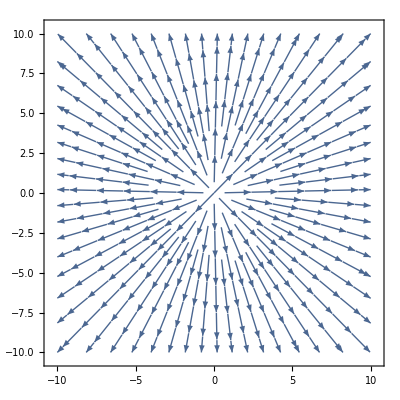

-Graphics3D-

```mathematica
StreamPlot[Evaluate[Grad[Sum[(-1)/Sqrt[((x-n)^2)+((y+n)^2)],{n,0,0}],{x,y}]],{x,-10,10},{y,-10,10}]
VectorPlot3D[Evaluate[Grad[(-1)/Sqrt[((x)^2)+((y)^2)+((z)^2)],{x,y,z}]],{x,-10,10},{y,-10,10},{z,-10,10}]
Animate[VectorPlot3D[Evaluate[Grad[(-1)/Sqrt[((x)^2)+((y)^2)+((z)^2)],{x,y,z}]],{x,-10,10},{y,-10,10},{z,-10,10}],{x,{0,1,2}},{y,{0,0,0}},{z,{0,0,0}}]
```

```mathematica
Animate[VectorPlot3D[Evaluate[Grad[(-1)/Sqrt[((x)^2)+((y)^2)+((z)^2)],{x,y,z}]],{x,-10,10},{y,-10,10},{z,-10,10},PlotRange->10],{x,{0,1,2}},{y,{0,0,0}},{z,{0,0,0}},AnimationRunning->False]
```

```mathematica
f[x_,y_,z_]:=Evaluate[Grad[(-1)/Sqrt[((x)^2)+((y)^2)+((z)^2)],{x,y,z}]];
```

```mathematica
g[x_,y_,z_,g_,m_,v_]:={((x)^2-m),x*y,x*z}*(g*v^2)/(2*(g^2*((x)^2-m)^2+(v*y)^2+(v*z)^2)^(3/2));

Animate[VectorPlot3D[f[x,y,z],{x,-5,5},{y,-5,5},{z,-5,5},PlotRange->5],{x,{0,1,2}},{y,{0,1,0}},{z,{0,1,0}},AnimationRunning->False]
```

```mathematica
Animate[VectorPlot3D[f[x,y,z],{x,-5,5},{y,-5,5},{z,-5,5},PlotRange->5],{x,{0,1,2,3,4}},{y,{0,1,2,3,4}},{z,{0,0,0,0,0}},AnimationRunning->True]
```

```mathematica
VectorPlot3D[f[x,y,z],{x,-5,5},{y,-5,5},{z,-5,5},PlotRange->5]
```

-Graphics3D-

```mathematica
ANIM=Table[VectorPlot3D[g[x,y,z,1,m,1],{x,-5,5},{y,-5,5},{z,-5,5},VectorColorFunction->Hue,PlotRange->5],{m,-5,5,0.25}];
Export["Test.gif",ANIM,ImageResolution->200]
```

Test.gif

```mathematica
Animate[Plot[Sin[a x]+Sin[b x],{x,0,10},PlotRange->2],{a,1,5},{b,1,5},AnimationRunning->True]
```

```mathematica
mymatrix=Transpose[{{0,1,2,3,4},{0,1,2,3,4},{0,1,2,3,4}}];
k[mymatrix[[1]]]
```

k[{0,0,0}]

```mathematica
k[anylist_list]:=Evaluate[Grad[(-1)/Sqrt[((x)^2)+((y)^2)+((z)^2)],{x,y,z}]]/.{x->anylist[[1]],y->anylist[[2]],z->anylist[[3]]};
```

```mathematica
Animate[VectorPlot3D[k[x,y,z],{x,-5,5},{y,-5,5},{z,-5,5},PlotRange->5],{x,{0,1,2,3,4}},{y,{0,1,2,3,4}},{z,{0,0,0,0,0}},AnimationRunning->True]
```

```mathematica
x+y/.{x->(thelist[[1]]),y->(thelist[[2]])}
```

9

```mathematica
VectorPlot[Evaluate[Grad[(-1)/Sqrt[((x)^2)+((y)^2)+((z)^2)],{x,y,z}]]/.{x->thelist[[1]],y->thelist[[2]],z->thelist[[3]]},{x,-5,5},{y,-5,5},{z,-5,5},PlotRange->5]
```

VectorPlot::nonopt: Options expected (instead of {z,-5,5}) beyond position 3 in VectorPlot[Evaluate[(]/.{x→thelist⟦1⟧,y→thelist⟦2⟧,z→thelist⟦3⟧},{x,-5,5},{y,-5,5},{z,-5,5},PlotRange→5]. An option must be a rule or a list of rules.

VectorPlot[Evaluate[(-1/(√(x^2+y^2+z^2))){x,y,z}]/.{x→thelist⟦1⟧,y→thelist⟦2⟧,z→thelist⟦3⟧},{x,-5,5},{y,-5,5},{z,-5,5},PlotRange→5]

```mathematica
thelist={4,5,6}
```

{4,5,6}

```mathematica
thelist[[1]]
```

0

```mathematica
Sum[Grad[(-1)/Sqrt[((x+n)^2)+((y)^2)],{x,y}],{n,0,2}]
```

{x/((x^2+y^2)^(3/2))+(1+x)/(((1+x)^2+y^2)^(3/2))+(2+x)/(((2+x)^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))+y/(((1+x)^2+y^2)^(3/2))+y/(((2+x)^2+y^2)^(3/2))}

```mathematica
Grad[Sum[(-1)/Sqrt[((x+n)^2)+((y)^2)],{n,0,2}],{x,y}]
```

{x/((x^2+y^2)^(3/2))+(1+x)/(((1+x)^2+y^2)^(3/2))+(2+x)/(((2+x)^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))+y/(((1+x)^2+y^2)^(3/2))+y/(((2+x)^2+y^2)^(3/2))}

```mathematica
pie=Evaluate[Grad[(-1)/Sqrt[((x)^2)+((y)^2)+((z)^2)],{x,y,z}]];pie=(pie/.{x->newx,y->newy,z->newz})
```

{newx/((newx^2+newy^2+newz^2)^(3/2)),newy/((newx^2+newy^2+newz^2)^(3/2)),newz/((newx^2+newy^2+newz^2)^(3/2))}

```mathematica
electricFieldFunction[mylist_List]:=Module[{},pie=Evaluate[Grad[(-1)/Sqrt[((x-nx)^2)+((y-ny)^2)+((z-nz)^2)],{x,y,z}]];pie=(pie/.{nx->mylist[[1]],ny->mylist[[2]],nz->mylist[[2]]});pie]
electricFieldFunction[{0,1,0}]
electricFieldFunction[mymatrix[[2]]]
```

{x/((x^2+(-1+y)^2+(-1+z)^2)^(3/2)),(-1+y)/((x^2+(-1+y)^2+(-1+z)^2)^(3/2)),(-1+z)/((x^2+(-1+y)^2+(-1+z)^2)^(3/2))}

{(-1+x)/(((-1+x)^2+(-1+y)^2+(-1+z)^2)^(3/2)),(-1+y)/(((-1+x)^2+(-1+y)^2+(-1+z)^2)^(3/2)),(-1+z)/(((-1+x)^2+(-1+y)^2+(-1+z)^2)^(3/2))}

```mathematica
VectorPlot3D[{x/((x^2+(-1+y)^2+z^2)^(3/2)),(-1+y)/((x^2+(-1+y)^2+z^2)^(3/2)),z/((x^2+(-1+y)^2+z^2)^(3/2))},{x,-5,5},{y,-5,5},{z,-5,5},PlotRange->5]
```

-Graphics3D-

```mathematica
sumFields[numCharges_Integer,numSteps_Integer,myArray_Array]:=Module[{n},vectorList=Evaluate[Sum[electricFieldFunction[myArray[[1]]],{n,0,numSteps}]]},{n,1,numCharges}]];vectorList]
```

```mathematica
sumFields[1,mymatrix]
```

sumFields[1,{{0,0,0},{1,1,1},{2,2,2},{3,3,3},{4,4,4}}]